## Objetos gráficos elementales

En Wolfram Language, Circle[ ] representa un círculo. Para mostrar el círculo en un gráfico se usa la función Graphics. Posteriormente se verá cómo especificar la posición y el tamaño de un círculo. Por ahora se describirá el manejo básico de un círculo, sin dar mayor detalle.

Muestre el gráfico de un círculo:

```mathematica
Graphics[Circle[ ]]
```

-Graphics-

Disk representa un disco rellenado:

```mathematica
Graphics[Disk[ ]]
```

-Graphics-

RegularPolygon es un polígono regular con cualquier número de lados que se desee.

Aquí se muestra un pentágono (un polígono regular con 5 lados):

```mathematica
Graphics[RegularPolygon[5]]
```

-Graphics-

Construya una tabla de los gráficos de los polígonos regulares que tienen entre 5 y 10 lados:

```mathematica
Table[Graphics[RegularPolygon[n]],{n,5,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Style funciona dentro de Graphics, así que puede utilizarse para colorear.

Aquí aparece un pentágono de color naranja:

```mathematica
Graphics[Style[RegularPolygon[5],Orange]]
```

-Graphics-

Wolfram Language trabaja en 3D igual que en 2D, con objetos como Sphere, Cylinder y Cone. Un gráfico 3D se puede hacer rotar de manera interactiva para tener diferentes ángulos de visión.

Muestre una esfera en 3D:

```mathematica
Graphics3D[Sphere[ ]]
```

-Graphics3D-

Una lista de un cono y un cilindro:

```mathematica
{Graphics3D[Cone[ ]],Graphics3D[Cylinder[ ]]}
```

{-Graphics3D-,-Graphics3D-}

Una esfera amarilla:

```mathematica
Graphics3D[Style[Sphere[ ],Yellow]]
```

-Graphics3D-

Vocabulario

Circle[ ] |   | especifica un círculo 
Disk[ ] |   | especifica un disco rellenado 
RegularPolygon[n] |   | especifica un polígono regular con n lados
Graphics[objeto] |   | muestra un objeto gráficamente 
Sphere[ ], Cylinder[ ], Cone[ ], ... |   | especifica formas geométricas en 3D 
Graphics3D[objeto] |   | muestra un objeto gráficamente en 3D

"8 Exercises Available"
"with 3 extras" | "Get Started »"

Use RegularPolygon para dibujar un triángulo. »

| Expected output: |  
  |  |

Dibuje el gráfico de un círculo rojo. »

| Expected output: |  
  |  |

Muestre un octágono rojo. »

| Expected output: |  
  |  |

Forme una lista cuyos elementos sean discos en tonalidades que varíen de 0 a 1 en incrementos de 0.1. »

| Expected output: |  
  | {,,,,,,,,,,} |

Muestre una columna con un triángulo rojo y otro verde. »

| Expected output: |  
  | 
 |

Presente una lista con los polígonos regulares que tengan de 5 a 10 lados, con cada polígono en color rosa. »

| Expected output: |  
  | {,,,,,} |

Muestre el gráfico de un cilindro morado. »

| Expected output: |  
  | -Graphics3D- |

Forme una lista de polígonos con 8, 7, 6, ... , 3 lados, coloreados aleatoriamente con RandomColor, y muéstrelo sobrepuestos con el triángulo arriba (sugerencia: aplicar Graphics a la lista). »

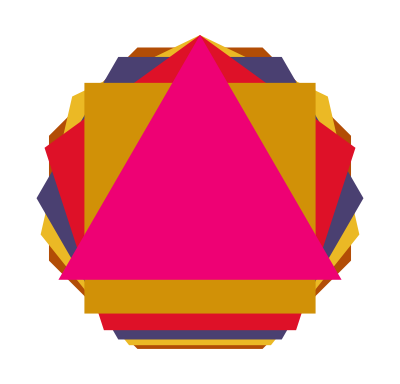
| Sample expected output: |  
  | -Graphics- |

Forme una lista de 10 pentágonos regulares coloreados de manera aleatoria.  »

| Expected output: |  
  | {,,,,,,,,,} |

Construya una lista con un polígono regular de 20 lados y un disco. »

| Expected output: |  
  | {,} |

Cree una lista de polígonos con 10, 9, ... , 3 lados. »

| Expected output: |  
  | {,,,,,,,} |

Preguntas y respuestas

¿Cómo se forma un gráfico que contenga varios objetos?

En la Sección 14 se explicará cómo, ya que para ello hay que haberse familiarizado con coordenadas.

¿Por qué se usa Circle[ ], en lugar de simplemente Circle?

Por razones de consistencia. Como se verá en la Sección 14, Circle[ ] es una versión abreviada de Circle[{0,0},1], que significa un círculo de radio 1, cuyo centro es el punto de coordenadas {0, 0}.

¿Por qué la esfera amarilla no tiene puro amarillo?

Porque Wolfram Language la muestra como si fuera un objeto real, con iluminación, en 3D. Si fuera solo amarillo no se vería la profundidad en 3D y aparecería como un disco en 2D.

Nota técnica

Otra forma de especificar estilos en gráficos es dar una lista de directivas, por ejemplo, {Yellow,Disk[ ],Black,Circle[ ]}.

Para explorar más

Guía para Graphics en Wolfram Language »